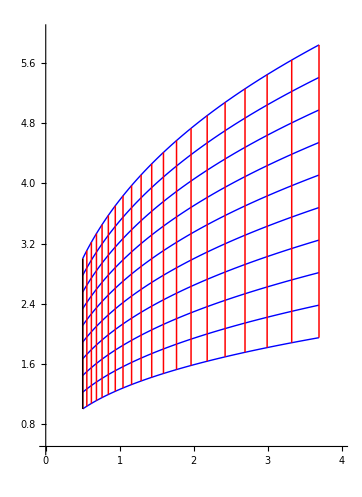

```mathematica
(* Initial Data *)
f =Log[x^2+y^2]/2+Log[(x-1)^2+(y-2)^2]/3;
U={D[f,x],D[f,y]};
U={x ,y/3};
γ=5{Cos[v],Sin[v]};
γ={1/2,v+2};

uCount=20;
uMin=0;
uMax=2;

v1=-1;
v2=1;
vCount=10;

xMin=0;
getSol[p0_,U_]:=Module[{Ut},
Ut=U/.{x->x[u],y->y[u]};
p={x[u],y[u]}/.NDSolve[{x'[u]==Ut[[1]],y'[u]==Ut[[2]],x[0]==p0[[1]],y[0]==p0[[2]]},{x,y},{u,0,10}];
p[[1]]
];

S[uVal_,ps_]:=Module[{},
{xs,ys}=Transpose[(ps/.u->uVal)];
vs=N[Table[v,{v,v1,v2,(v2-v1)/(vCount-1)}]];
xs = Interpolation[Transpose[{vs,xs}]];
ys = Interpolation[Transpose[{vs,ys}]];
np={xs[v],ys[v]}
];

xMin=0;
xMax=4;
yMin=1/2;
yMax=6;
pr ={{xMin,xMax},{yMin,yMax}};
ps=Table[getSol[γ,U],{v,v1,v2,(v2-v1)/(vCount-1)}];
fG=ParametricPlot[ps,{u,uMin,uMax},PlotRange->pr,PlotStyle->Directive[Blue,Thick]];
γG=ParametricPlot[γ,{v,v1,v2},PlotStyle->Directive[Black,Thick]];

ss=Table[S[u,ps],{u,uMin,uMax,(uMax-uMin)/(uCount-1)}];
sG=ParametricPlot[ss,{v,v1,v2},PlotRange->pr,PlotStyle->Directive[Red,Thickness[.003]]];
stG=StreamPlot[U,{x,xMin,xMax},{y,yMin,yMax}];
Show[fG,sG,γG,Axes->True]
```